```mathematica
p=IdentityMatrix[9]-IdentityMatrix[9]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
p[[1,7]]=.5;
p[[1,5]]=.5;

p[[4,5]]=.5;
p[[4,1]]=.5;

p[[5,1]]=.5;
p[[5,7]]=.5;

p[[7,4]]=.5;
p[[7,9]]=.5;

p[[9,9]]=1;
```

```mathematica
p//MatrixForm
```

(0 | 0 | 0 | 0 | 0.5 | 0 | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Drop[p,{8},{8}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0.5 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
p=Drop[%,{2,3},{2,3}]
```

{{0,0,0.5,0,0.5,0},{0.5,0,0.5,0,0,0},{0.5,0,0,0,0.5,0},{0,0,0,0,0,0},{0,0.5,0,0,0,0.5},{0,0,0,0,0,1}}

```mathematica
p//MatrixForm
```

(0 | 0 | 0.5 | 0 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0 | 0
0.5 | 0 | 0 | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
p={{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0,0,0,0,1}}
```

{{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0,0,0,0,1}}

```mathematica
p//MatrixForm
```

```mathematica
(   {{1, 4, 5, 7, 9}}   )
({{1}, {4}, {5}, {7}, {9}})({{0, 0, 0.5, 0.5, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 1}})
```

```mathematica
d=DiscreteMarkovProcess[1,p]
```

DiscreteMarkovProcess[1,{{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{0,0,0,0,1}}]

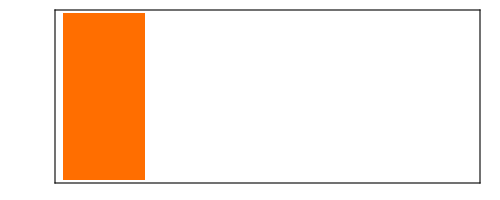
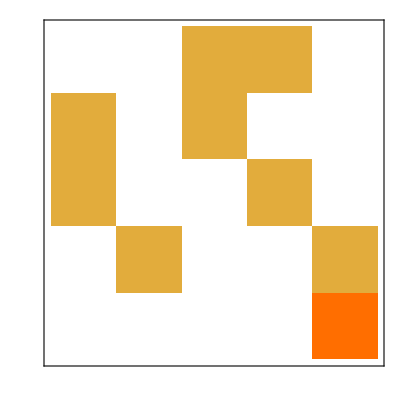
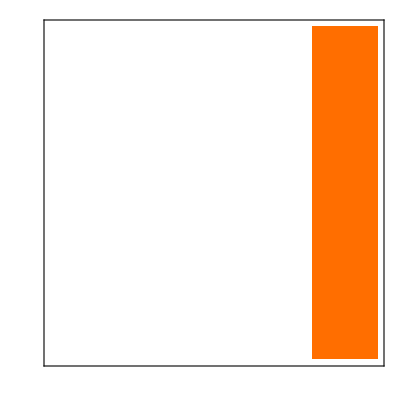
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0,0,0,∞}
HoldingTimeVariance | {0,0,0,0,∞}
Structural Properties | 
CommunicatingClasses | {5}, {1,…,4}
RecurrentClasses | {5}
TransientClasses | {1,…,4}
AbsorbingClasses | {5}
PeriodicClasses | None
Periods | {}
Irreducible | False
Primitive | False
Aperiodic | True
Transient Properties | 
TransientVisitMean | {2.33333,1.,1.66667,2.}
TransientVisitVariance | {22.8889,28.6667,26.2222,24.6667}
TransientTotalVisitMean | 3.21429
Limiting Properties | 
ReachabilityProbability | {0.571429,0.5,0.714286,1.,1.}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[d]
```

```mathematica
firstpassdist=FirstPassageTimeDistribution[DiscreteMarkovProcess[1,({{0, 0, 0.5, 0.5, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 1}})],5];
```

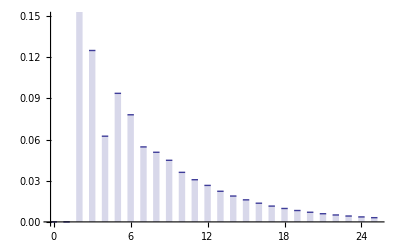

```mathematica
DiscretePlot[PDF[firstpassdist,k],{k,0,25},ExtentSize->.5]
```

```mathematica
Mean[firstpassdist]
```

7.

```mathematica
p//MatrixForm
```

```mathematica
"number 1"
```

number 1

```mathematica
Solve[{({{p1-0.5 p5-0.5 p7}, {-0.5 p1+p4-0.5 p5}, {-0.5 p1+p5-0.5 p7}, {-0.5 p4+p7-0.5 0}, {0}})==Transpose[{{1,1,1,1,0}}]},{p1,p4,p5,p7}]
```

{{p1→7.,p4→8.,p5→7.,p7→5.}}

```mathematica
Mean[{7,8,7,5}]//N
```

6.75

```mathematica
"number 2"
```

number 2

```mathematica
pabsord//MatrixForm
```

(0 | 0 | 0.5 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0
0.5 | 0 | 0 | 0.5 | 0
0 | 0.5 | 0 | 0 | 0.5
0 | 0 | 0 | 0 | 1)

```mathematica
Solve[{(({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}})-({{0, 0, 0, 0, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0, 0, 0, 0, 0}})).Transpose[{{p1,p4,p5,p7,p9}}]==Transpose[{{0,0,0,0,1}}]},{p1,p4,p5,p7,p9}]//ReleaseHold
```

{{p1→0.,p4→0.142857,p5→0.285714,p7→0.571429,p9→1.}}

```mathematica
"number 3"
```

```mathematica
pp={{0,0,0.5,0.5,0},{0.5,0,0.5,0,0},{0.5,0,0,0.5,0},{0,0.5,0,0,0.5},{.5,0,0,.5,0}};
```

```mathematica
pp//MatrixForm
```

(0 | 0 | 0.5 | 0.5 | 0
0.5 | 0 | 0.5 | 0 | 0
0.5 | 0 | 0 | 0.5 | 0
0 | 0.5 | 0 | 0 | 0.5
0.5 | 0 | 0 | 0.5 | 0)

```mathematica
dd=DiscreteMarkovProcess[1,pp]
```

```mathematica
Graph[dd]
```

```mathematica
"irreducible, finite, stationary distribution, aperiodic because 3->1->3 and 3->4->2->3 hence limiting = stationary"
```

-Graphics-

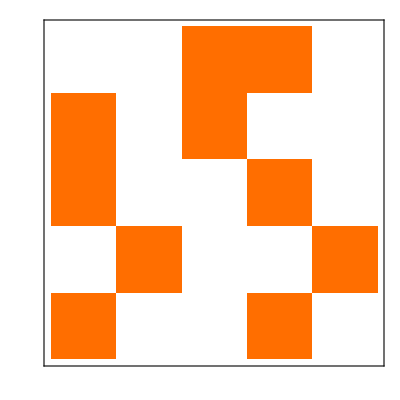
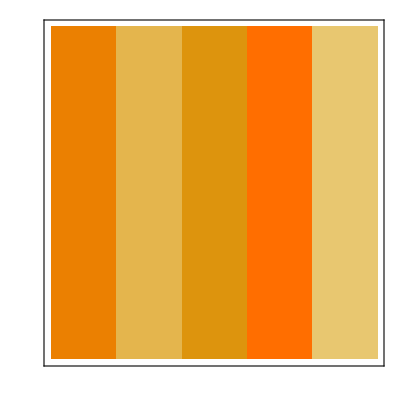
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0,0,0,0,0}
HoldingTimeVariance | {0,0,0,0,0}
Structural Properties | 
CommunicatingClasses | {1,…,5}
RecurrentClasses | {1,…,5}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
MarkovProcessProperties[dd]
```

```mathematica
MatrixPower[pp,100]//MatrixForm
```

(0.238095 | 0.142857 | 0.190476 | 0.285714 | 0.142857
0.238095 | 0.142857 | 0.190476 | 0.285714 | 0.142857
0.238095 | 0.142857 | 0.190476 | 0.285714 | 0.142857
0.238095 | 0.142857 | 0.190476 | 0.285714 | 0.142857
0.238095 | 0.142857 | 0.190476 | 0.285714 | 0.142857)

```mathematica
"probability of returning to 1 if you've hit 1"
```

```mathematica
Solve[{(({{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}})-({{0, 0, 0, 0, 0}, {0.5, 0, 0.5, 0, 0}, {0.5, 0, 0, 0.5, 0}, {0, 0.5, 0, 0, 0.5}, {0.5, 0, 0, 0.5, 0}})).Transpose[{{p1,p4,p5,p7,p9}}]==Transpose[{{1,1,1,1,1}}]},{p1,p4,p5,p7,p9}]//ReleaseHold
```

{{p1→1.,p4→3.4,p5→3.8,p7→4.6,p9→3.8}}